## Flight-gate problem

Бронников Егор ПМ-1901

### Данные

```mathematica
numberOfFlights = 10;
numberOfGates=3;
maxTimeStart=100;
tmin=3;
landing:=RandomInteger[{5,10}]
tow:=RandomInteger[{3,5}]
parking:=RandomInteger[{5,15}]
```

```mathematica
Clear[getArrivalInterval]
getArrivalInterval[time_]:={time,time+landing}
```

```mathematica
Clear[getParkingInterval]
getParkingInterval[arr:{_,time_}]:={arr,{#,#+parking}&[time+tow]}
```

```mathematica
Clear[getDepartureInterval]
getDepartureInterval[{arr_,park:{_,time_}}]:={arr,park,{#,#+landing}&[time+tow]}
```

```mathematica
Composition[getDepartureInterval,getParkingInterval,getArrivalInterval][10](*1 список - arrival, 2 список - parking,
3 список - departure*)
```

{{10,15},{19,24},{29,38}}

```mathematica
timeIntervals=Table[
Composition[RandomChoice[{0.8,0.2}->{getDepartureInterval,Identity}],getParkingInterval,getArrivalInterval]@RandomInteger[{0,maxTimeStart}],
numberOfFlights
];
```

```mathematica
timeIntervals
```

{{{99,104},{107,118}},{{54,63},{67,78},{83,89}},{{25,30},{33,42}},{{82,87},{90,101},{105,113}},{{79,84},{88,96}},{{84,94},{98,105},{109,115}},{{36,43},{48,59},{62,69}},{{12,18},{21,26},{29,39}},{{36,44},{49,61}},{{49,59},{64,77},{82,91}}}

```mathematica
maxTime=Max@timeIntervals;
```

```mathematica
events=TakeList[Range@Length@Flatten[#,1],Length/@#]&@timeIntervals;
```

```mathematica
events
```

{{1,2},{3,4,5},{6,7},{8,9,10},{11,12},{13,14,15},{16,17,18},{19,20,21},{22,23},{24,25,26}}

```mathematica
pf=RandomInteger[{1,20},numberOfGates]&/@Flatten[events];
```

```mathematica
pf
```

{{6,10,6},{8,14,19},{7,17,13},{10,17,6},{10,20,15},{6,16,19},{12,3,10},{13,16,7},{3,11,3},{12,9,5},{14,13,1},{19,11,12},{18,5,9},{3,3,6},{20,1,8},{15,1,4},{13,16,10},{7,7,16},{10,14,19},{12,3,13},{13,5,9},{1,2,1},{19,3,10},{18,11,2},{4,9,2},{16,13,6}}

M(i) ∀ i ∈ N (допустимые гейты)

```mathematica
posPref=Flatten[RandomSample[#,RandomInteger[{0,Length@#-1}]]&/@MapIndexed[#2&,pf,{2}],1];
```

```mathematica
posPref
```

{{2,3},{3,1},{5,2},{6,2},{6,1},{10,2},{10,1},{11,3},{12,2},{13,3},{14,1},{17,2},{18,3},{18,2},{19,2},{19,3},{20,1},{21,2},{22,3},{22,1},{23,1},{23,3},{24,3}}

```mathematica
preferences=ReplacePart[pf,posPref->-∞];
```

```mathematica
preferences
```

{{6,10,6},{8,14,-∞},{-∞,17,13},{10,17,6},{10,-∞,15},{-∞,-∞,19},{12,3,10},{13,16,7},{3,11,3},{-∞,-∞,5},{14,13,-∞},{19,-∞,12},{18,5,-∞},{-∞,3,6},{20,1,8},{15,1,4},{13,-∞,10},{7,-∞,-∞},{10,-∞,-∞},{-∞,3,13},{13,-∞,9},{-∞,2,-∞},{-∞,3,-∞},{18,11,-∞},{4,9,2},{16,13,6}}

```mathematica
assoc=AssociationThread[Flatten[events],Flatten[timeIntervals,1]]
```

<|1→{99,104},2→{107,118},3→{54,63},4→{67,78},5→{83,89},6→{25,30},7→{33,42},8→{82,87},9→{90,101},10→{105,113},11→{79,84},12→{88,96},13→{84,94},14→{98,105},15→{109,115},16→{36,43},17→{48,59},18→{62,69},19→{12,18},20→{21,26},21→{29,39},22→{36,44},23→{49,61},24→{49,59},25→{64,77},26→{82,91}|>

Буфферное время между двумя событиями

```mathematica
Clear[getTimeGap]
getTimeGap[{{arr1_,dep1_},{arr2_,dep2_}}]:=Max[arr2-dep1,arr1-dep2]
```

Если отрицательное число, то это означает что два события не могут быть назначены на 1 гейт

```mathematica
getTimeGap[{{21,31},{25,30}}]
```

-6

```mathematica
f=getTimeGap@Lookup[assoc,{#1,#2}]&;
```

```mathematica
Lookup[assoc,{1,2}]
```

{{99,104},{107,118}}

```mathematica
dm=DistanceMatrix[Flatten[events],DistanceFunction->HoldPattern[f]]/.Abs[z_]:>ReleaseHold[z];
```

```mathematica
dm2=dm SparseArray[{i_,i_}->0,Dimensions@dm,1];
```

```mathematica
(dm2⟦##⟧=tmin)&@@@Flatten[Partition[#,2,1]&/@events,1];
```

```mathematica
events
```

{{1,2},{3,4,5},{6,7},{8,9,10},{11,12},{13,14,15},{16,17,18},{19,20,21},{22,23},{24,25,26}}

```mathematica
Flatten[Partition[#,2,1]&/@events,1]
```

{{1,2},{3,4},{4,5},{6,7},{8,9},{9,10},{11,12},{13,14},{14,15},{16,17},{17,18},{19,20},{20,21},{22,23},{24,25},{25,26}}

Матрица с буфферным временем, которое t

```mathematica
distanceMatrix=#+#ᵀ&@UpperTriangularize[dm2];
```

```mathematica
events
timeIntervals
preferences
distanceMatrix
```

{{1,2},{3,4,5},{6,7},{8,9,10},{11,12},{13,14,15},{16,17,18},{19,20,21},{22,23},{24,25,26}}

{{{99,104},{107,118}},{{54,63},{67,78},{83,89}},{{25,30},{33,42}},{{82,87},{90,101},{105,113}},{{79,84},{88,96}},{{84,94},{98,105},{109,115}},{{36,43},{48,59},{62,69}},{{12,18},{21,26},{29,39}},{{36,44},{49,61}},{{49,59},{64,77},{82,91}}}

{{6,10,6},{8,14,-∞},{-∞,17,13},{10,17,6},{10,-∞,15},{-∞,-∞,19},{12,3,10},{13,16,7},{3,11,3},{-∞,-∞,5},{14,13,-∞},{19,-∞,12},{18,5,-∞},{-∞,3,6},{20,1,8},{15,1,4},{13,-∞,10},{7,-∞,-∞},{10,-∞,-∞},{-∞,3,13},{13,-∞,9},{-∞,2,-∞},{-∞,3,-∞},{18,11,-∞},{4,9,2},{16,13,6}}

{{0,3,36,21,10,69,57,12,-2,1,15,3,5,-6,5,56,40,30,81,73,60,55,38,40,22,8},{3,0,44,29,18,77,65,20,6,-6,23,11,13,2,-8,64,48,38,89,81,68,63,46,48,30,16},{36,44,0,3,20,24,12,19,27,42,16,25,21,35,46,11,-5,-1,36,28,15,10,-7,-5,1,19},{21,29,3,0,3,37,25,4,12,27,1,10,6,20,31,24,8,-2,49,41,28,23,6,8,-10,4},{10,18,20,3,0,53,41,-4,1,16,-1,-1,-5,9,20,40,24,14,65,57,44,39,22,24,6,-7},{69,77,24,37,53,0,3,52,60,75,49,58,54,68,79,6,18,32,7,-1,-1,6,19,19,34,52},{57,65,12,25,41,3,0,40,48,63,37,46,42,56,67,-6,6,20,15,7,-6,-6,7,7,22,40},{12,20,19,4,-4,52,40,0,3,18,-2,1,-3,11,22,39,23,13,64,56,43,38,21,23,5,-5},{-2,6,27,12,1,60,48,3,0,3,6,-6,-4,-3,8,47,31,21,72,64,51,46,29,31,13,-1},{1,-6,42,27,16,75,63,18,3,0,21,9,11,0,-4,62,46,36,87,79,66,61,44,46,28,14},{15,23,16,1,-1,49,37,-2,6,21,0,3,0,14,25,36,20,10,61,53,40,35,18,20,2,-2},{3,11,25,10,-1,58,46,1,-6,9,3,0,-6,2,13,45,29,19,70,62,49,44,27,29,11,-3},{5,13,21,6,-5,54,42,-3,-4,11,0,-6,0,3,15,41,25,15,66,58,45,40,23,25,7,-7},{-6,2,35,20,9,68,56,11,-3,0,14,2,3,0,3,55,39,29,80,72,59,54,37,39,21,7},{5,-8,46,31,20,79,67,22,8,-4,25,13,15,3,0,66,50,40,91,83,70,65,48,50,32,18},{56,64,11,24,40,6,-6,39,47,62,36,45,41,55,66,0,3,19,18,10,-3,-7,6,6,21,39},{40,48,-5,8,24,18,6,23,31,46,20,29,25,39,50,3,0,3,30,22,9,4,-10,-10,5,23},{30,38,-1,-2,14,32,20,13,21,36,10,19,15,29,40,19,3,0,44,36,23,18,1,3,-5,13},{81,89,36,49,65,7,15,64,72,87,61,70,66,80,91,18,30,44,0,3,11,18,31,31,46,64},{73,81,28,41,57,-1,7,56,64,79,53,62,58,72,83,10,22,36,3,0,3,10,23,23,38,56},{60,68,15,28,44,-1,-6,43,51,66,40,49,45,59,70,-3,9,23,11,3,0,-3,10,10,25,43},{55,63,10,23,39,6,-6,38,46,61,35,44,40,54,65,-7,4,18,18,10,-3,0,3,5,20,38},{38,46,-7,6,22,19,7,21,29,44,18,27,23,37,48,6,-10,1,31,23,10,3,0,-10,3,21},{40,48,-5,8,24,19,7,23,31,46,20,29,25,39,50,6,-10,3,31,23,10,5,-10,0,3,23},{22,30,1,-10,6,34,22,5,13,28,2,11,7,21,32,21,5,-5,46,38,25,20,3,3,0,3},{8,16,19,4,-7,52,40,-5,-1,14,-2,-3,-7,7,18,39,23,13,64,56,43,38,21,23,3,0}}

### Создание исходного графа

```mathematica
numberOfEvents=Length[Flatten@events];
```

```mathematica
verticesGatesShape=#->"Square"&/@Range[numberOfEvents+1,numberOfEvents+numberOfGates];
verticesGatesColor=#->Darker[Red]&/@Range[numberOfEvents+1,numberOfEvents+numberOfGates];
```

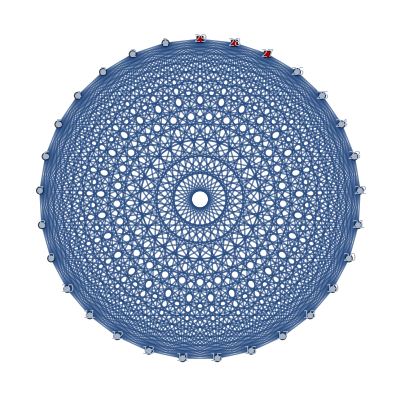

```mathematica
graph=CompleteGraph[numberOfEvents+numberOfGates,
VertexShapeFunction->verticesGatesShape,
VertexSize->0.2,
VertexStyle->verticesGatesColor,
VertexLabels->Placed["Name",Center]]
```

```mathematica
edgeList=DeleteDuplicates[SortBy[List@@@EdgeList[graph],First]];
```

```mathematica
vertexList=VertexList[graph];
```

```mathematica
alpha1=10;
alpha2=20;
alpha3=30;
```

### Определения предка события

```mathematica
successorsPairs=Flatten[Partition[#,2,1]&/@events,1]
```

{{1,2},{3,4},{4,5},{6,7},{8,9},{9,10},{11,12},{13,14},{14,15},{16,17},{17,18},{19,20},{20,21},{22,23},{24,25},{25,26}}

```mathematica
Clear[u,event,successor]

Do[
{successor,event}=pair;
u[event]=successor,
{pair,successorsPairs}
]
```

### Определение веса

```mathematica
Clear[getWeightMatrix]
getWeightMatrix[{vertexList_:vertexList,edgeList_:edgeList},
			u_:u,
			{tmin_:tmin,numberOfEvents_:numberOfEvents,distanceMatrix_:distanceMatrix,preferences_:preferences},
			{alpha1_:alpha1,alpha2_:alpha2,alpha3_:alpha3}]:=Module[
{
weightMatrix=SparseArray[{{i_,j_}:>0},{Length[vertexList],Length[vertexList]}],
i,j
},
Do[
{i,j}=edge;
If[
i<=numberOfEvents∧j<=numberOfEvents,
If[
distanceMatrix⟦i,j⟧<0,
weightMatrix⟦i,j⟧=-∞,
If[
distanceMatrix⟦i,j⟧>=0∧(u[i]===j∨u[j]===i),
weightMatrix⟦i,j⟧=alpha2,
If[
distanceMatrix⟦i,j⟧>=0∧u[i]=!=u[j]∧u[j]=!=u[i],
weightMatrix⟦i,j⟧=alpha3*Max[tmin-distanceMatrix⟦i,j⟧,0]
]
]
],
If[
i<=numberOfEvents∧j>numberOfEvents,
If[
preferences⟦i,j-numberOfEvents⟧==-∞,
weightMatrix⟦i,j⟧=-∞,
weightMatrix⟦i,j⟧=alpha1*preferences⟦i,j-numberOfEvents⟧
],
weightMatrix⟦i,j⟧=-∞
]
],
{edge,edgeList}
];
weightMatrix
]
```

```mathematica
weightMatrix=getWeightMatrix[{vertexList,edgeList},u,{tmin,numberOfEvents,distanceMatrix,preferences},{alpha1,alpha2,alpha3}];
```

```mathematica
fullWeightMatrix=#+#ᵀ&@UpperTriangularize[weightMatrix];
```

### Целевая функция

```mathematica
Clear[targetFunction]
targetFunction[solution_,weightMatrix_]:=Module[
{
cliqueEdges=Partition[#,2,1,1]&/@solution
},
Total[Apply[fullWeightMatrix⟦##⟧&,cliqueEdges,{2}],2]
]
```

### Детерминированное начальное разбиение

```mathematica
Clear[h]
h[i_,C_,D_]:=Subtract@@Composition[Total,Map[fullWeightMatrix⟦i,#⟧&,#]&]/@{D,Complement[C,{i}]}
```

```mathematica
Clear[getAssignmentData]
getAssignmentData[clique_,nontabu_,u_,h_]:=Module[
{
currentSum,currentC,prevC,prevPrevC,
maxSum=-∞,maxVertex=0,maxD={}
},
Do[
currentC=clique⟦FirstPosition[clique,i]⟦1⟧⟧;
prevC=clique⟦FirstPosition[clique,u[i]]⟦1⟧⟧;
prevPrevC=clique⟦FirstPosition[clique,u[u[i]]]⟦1⟧⟧;
currentSum=h[i,currentC,D]+h[u[i],prevC,D]+h[u[u[i]],prevPrevC,D];
If[
currentSum>maxSum,
maxSum=currentSum;
maxVertex=i;
maxD=D;
],
{i,nontabu},
{D,clique}
];
{maxSum,maxVertex,maxD}
]
```

```mathematica
Clear[initialSolution]
initialSolution[vertexList_,u_,h_]:=Module[
{
clique=Partition[vertexList,1,1],
mask=Thread[And[Composition[NumberQ,u,u]/@vertexList,Composition[NumberQ,u]/@vertexList]],
tabu,nontabu,
maxSum,maxVertex,maxD,maxVertices,value
},
nontabu=Pick[vertexList,mask];
tabu=Complement[vertexList,nontabu];
While[
nontabu=!={},
{maxSum,maxVertex,maxD}=getAssignmentData[clique,nontabu,u,h];
If[
maxSum>0,
{maxSum,maxVertex,maxD}=getAssignmentData[clique,nontabu,u,h];
maxVertices={maxVertex,u[maxVertex],u[u[maxVertex]]};
value=DeleteDuplicates[clique⟦FirstPosition[clique,maxD]⟦1⟧⟧~Join~maxVertices];
clique⟦FirstPosition[clique,maxD]⟦1⟧⟧=value;
clique=DeleteCases[#,x_/;AnyTrue[value,x==#&]]&/@Complement[clique,value];
AppendTo[clique,value];
];
nontabu=DeleteCases[nontabu,maxVertex];
AppendTo[tabu,maxVertex];
];
DeleteCases[Sort/@clique,{}]
]
```

```mathematica
feasibleSolution=initialSolution[vertexList,u,h]
targetFunction[feasibleSolution,fullWeightMatrix]
```

{{1},{2},{6},{7},{12},{22},{23},{28},{8,9,10},{16,17,18},{11,13,14,15},{24,25,26,27},{3,4,5,29},{19,20,21}}

950

### Случайное начальное разбиение

```mathematica
Clear[randomInitialSolution]
randomInitialSolution[vertexList_,maxNumberInPart_:10,weightMatrix_]:=Module[
{
vertexCount=Length[vertexList],
shuffle=RandomSample[vertexList],
random,
cliques={},
i=1
},
While[i<vertexCount,
random=RandomInteger[Quotient[vertexCount,maxNumberInPart]];
If[i+random<vertexCount,
AppendTo[cliques,shuffle⟦i;;i+random⟧];
i+=random+1,
AppendTo[cliques,shuffle⟦i;;vertexCount⟧];
i=vertexCount]
];
If[Length[Flatten[cliques]]!=vertexCount∨targetFunction[cliques,weightMatrix]==-∞,
randomInitialSolution[vertexList,maxNumberInPart,weightMatrix],
cliques]
]
```

```mathematica
randomSolution=randomInitialSolution[vertexList,fullWeightMatrix]
```

{{18,27},{23},{19,26},{21},{5,3},{6},{7},{16,25},{22,10},{14,4},{13},{29,15},{8,17,1},{12},{11,2,9},{20},{24,28}}

### Сравнение начальных разбиений (самоутверждение)

```mathematica
feasibleTFValue=targetFunction[feasibleSolution,fullWeightMatrix];
randomTFValue=targetFunction[randomSolution,fullWeightMatrix];

Style[
Grid[
{{"Название","Значение ЦФ"},
{"Детерминированное НР",feasibleTFValue},
{"Случайное НР",randomTFValue},
Style[#,Red]&/@{"∆",feasibleTFValue-randomTFValue}},
Frame->All,
Background->{None,{LightPurple}}],
FontSize->16,FontFamily->"Times New Roman"]
```

Название | Значение ЦФ
Детерминированное НР | 950
Случайное НР | 520
∆ | 430

### Алгоритм локального поиска

```mathematica
Clear[localSearch]
localSearch[solution_,numberOfIterations_,vertexList_,weightMatrix_]:=Module[
{
currentSolution=solution,
candidateSolution,
cliqueVariants,withoutVertex,selectedVertex,
cliquesTargetFunctionValue,
maxElementPosition,maxTargetFunctionValue
},
Do[
selectedVertex=RandomChoice[vertexList];
cliqueVariants=Table[
withoutVertex=Append[DeleteCases[currentSolution,selectedVertex,{2}],{}];
AppendTo[withoutVertex⟦i⟧,selectedVertex];
withoutVertex,
{i,Length[currentSolution]+1}];
cliquesTargetFunctionValue=targetFunction[#,weightMatrix]&/@cliqueVariants;
maxTargetFunctionValue=Max[cliquesTargetFunctionValue];
If[maxTargetFunctionValue!=-∞,
maxElementPosition=FirstPosition[cliquesTargetFunctionValue,Max[maxTargetFunctionValue]]⟦1⟧;
candidateSolution=DeleteCases[cliqueVariants⟦maxElementPosition⟧,{}];
If[maxTargetFunctionValue>targetFunction[currentSolution,weightMatrix],
currentSolution=candidateSolution],
Continue[]],
numberOfIterations];
currentSolution
]
```

```mathematica
localSearchSolution=localSearch[feasibleSolution,1000,vertexList,fullWeightMatrix]
targetFunction[localSearchSolution,fullWeightMatrix]
```

{{1,2},{6,29},{7,26},{12,27},{22},{28,3,4},{8},{16,17,18,23},{11,13},{24,25},{5,9,10,14,15},{19,20,21}}

1710

### Алгоритм имитации отжига

Функции изменения температуры

```mathematica
Clear[logarithmicSchedule]
Options[logarithmicSchedule]={CoolingSpeed->1.(*>=1*)};
logarithmicSchedule[temp_?NumberQ,iteration_,OptionsPattern[]]:=temp/(OptionValue[CoolingSpeed] Log[iteration+1]+1)
```

```mathematica
Clear[geometricSchedule]
Options[geometricSchedule]={CoolingSpeed->0.85(*[0.8,0.9]*)};
geometricSchedule[temp_?NumberQ,iteration_,OptionsPattern[]]:=OptionValue[CoolingSpeed]^iteration temp
```

```mathematica
Clear[linearSchedule]
Options[linearSchedule]={CoolingSpeed->0.85(*>0*)};
linearSchedule[temp_?NumberQ,iteration_,OptionsPattern[]]:=temp/(1+OptionValue[CoolingSpeed] iteration)
```

```mathematica
Clear[quadraticSchedule]
Options[quadraticSchedule]={CoolingSpeed->0.85(*>0*)};
quadraticSchedule[temp_?NumberQ,iteration_,OptionsPattern[]]:=temp/(1+OptionValue[CoolingSpeed] iteration^2)
```

```mathematica
Clear[getCandidate]
getCandidate[currentSolution_,selectedVertex_,weightMatrix_]:=Module[
{
cliqueVariants,
withoutVertex,
candidateSolution
},
While[True,
cliqueVariants=Table[
withoutVertex=Append[DeleteCases[currentSolution,selectedVertex,{2}],{}];
AppendTo[withoutVertex⟦i⟧,selectedVertex];
withoutVertex,
{i,Length[currentSolution]+1}];
If[AllTrue[targetFunction[#,weightMatrix]&/@cliqueVariants,#==-∞&],
Print["Stop by wrong vertex"];
Break[]];
candidateSolution=DeleteCases[RandomChoice[cliqueVariants],{}];
If[targetFunction[candidateSolution,weightMatrix]!=-∞,Break[]];
];
candidateSolution
]
```

```mathematica
Clear[simulatedAnnealing]
simulatedAnnealing[solution_,{tMin_,tMax_,temperatureFunction_,coolingSpeed_},vertexList_,weightMatrix_]:=Module[
{
tCurrent=tMax,
currentSolution=solution,
selectedVertex,withoutVertex,cliqueVariants,candidateSolution,
differenceTargetFunctions,i=1
},
While[tCurrent>tMin,
selectedVertex=RandomChoice[vertexList];
candidateSolution=getCandidate[currentSolution,selectedVertex,weightMatrix];
differenceTargetFunctions=targetFunction[candidateSolution,weightMatrix]-targetFunction[currentSolution,weightMatrix];
If[differenceTargetFunctions>0,
currentSolution=candidateSolution,
If[RandomReal[]<Exp[differenceTargetFunctions/tCurrent],
currentSolution=candidateSolution]
];
tCurrent=temperatureFunction[tCurrent,i,CoolingSpeed->coolingSpeed];
i+=1;
];
currentSolution
]
```

```mathematica
feasibleSolution
targetFunction[feasibleSolution,fullWeightMatrix]
```

{{1},{2},{6},{7},{12},{22},{23},{28},{8,9,10},{16,17,18},{11,13,14,15},{24,25,26,27},{3,4,5,29},{19,20,21}}

950

```mathematica
simulatedAnnealingSolution=Quiet@simulatedAnnealing[feasibleSolution,{0.01,150,logarithmicSchedule,1.5},vertexList,fullWeightMatrix]
targetFunction[simulatedAnnealingSolution,fullWeightMatrix]
```

{{1},{2},{6},{7},{12},{22},{23},{28,20},{8,9,10,18},{16,17},{11,13,14,15},{24,25,26,27},{3,4,5,29},{19,21}}

970

### Алгоритм поиска с запретом

```mathematica
Clear[getCandidateList]
getCandidateList[currentSolution_,vertexList_]:=Module[
{
withoutVertex
},
Table[
Table[
withoutVertex=Append[DeleteCases[currentSolution,v,{2}],{}];
AppendTo[withoutVertex⟦i⟧,v];
DeleteCases[withoutVertex,{}],
{i,Length[currentSolution]+1}],
{v,vertexList}]
]
```

```mathematica
Clear[getDifferenceMatrix]
getDifferenceMatrix[currentSolution_,candidateList_,weightMatrix_]:=Map[targetFunction[#,weightMatrix]-targetFunction[currentSolution,weightMatrix]&,candidateList,{2}]
```

```mathematica
Clear[tabuSearch]
tabuSearch[solution_,numberOfIterations_,lenTS_,vertexList_,weightMatrix_]:=Module[
{
currentSolution=solution,
candidateList,candidateSolution,
M,
vertex,clique,
tabu={},
i=1
},
While[i<numberOfIterations∧Length[tabu]<lenTS,
candidateList=getCandidateList[currentSolution,vertexList];
M=getDifferenceMatrix[currentSolution,candidateList,weightMatrix];
If[Max[M]<=0,
Print["Stop by nonpositive difference"];
Break[],
{vertex,clique}=FirstPosition[M,Max[M]]
];
candidateSolution=candidateList⟦vertex,clique⟧;
While[candidateList!={}∧MemberQ[candidateSolution,tabu],
candidateList=DeleteCases[candidateList,candidateSolution,{2}];
M=getDifferenceMatrix[currentSolution,candidateList,weightMatrix];
If[Max[M]<=0,
Print["Stop by nonpositive difference"];
Break[],
{vertex,clique}=FirstPosition[M,Max[M]]
];
candidateSolution=candidateList⟦vertex,clique⟧;
If[candidateList=={}∨!MemberQ[candidateSolution,tabu],Break[]]
];
currentSolution=candidateSolution;
AppendTo[tabu,candidateSolution]
];
currentSolution
]
```

```mathematica
tabuSearchSolution=tabuSearch[feasibleSolution,30,10,vertexList,fullWeightMatrix]
```

{{1,10},{2,14},{6,29},{7},{12,27,15},{22},{23,18},{28,8},{9,5},{16,17},{11,13,4},{24,26},{3,25},{19,20,21}}

```mathematica
targetFunction[tabuSearchSolution,fullWeightMatrix]
targetFunction[feasibleSolution,fullWeightMatrix]
```

1860

950

### Подбор гиперпараметров

#### GridSearch

```mathematica
Clear[GridSearch]
Options[GridSearch]={OneParameterIteration->1};
GridSearch[function_Symbol,args_List,parameters_Association,fullWeightMatrix_,OptionsPattern[]]:=Module[
{
parameterNames=Keys[parameters],
parameterValues=Values[parameters],
parametersList,
currentParamsValue,
bestParamsValue=-∞,bestParams
},
parametersList=Thread[parameterNames->#]&/@DeleteDuplicates[Flatten[Outer[List,Sequence@@parameterValues],2]];
Do[
currentParamsValue=Mean[Table[targetFunction[function[Sequence@@args,Sequence@@params],fullWeightMatrix],OptionValue[OneParameterIteration]]];
If[
currentParamsValue>bestParamsValue,
bestParamsValue=currentParamsValue;
bestParams=params
],
{params,parametersList}
];
{bestParams,N[bestParamsValue]}
]
```

#### Алгоритм имитации отжига

```mathematica
Clear[simulatedAnnealingGridSearch]
Options[simulatedAnnealingGridSearch]={tMin->0.5,tMax->10,CoolingSpeed->1};
simulatedAnnealingGridSearch[solution_,temperatureFunction_,vertexList_,weightMatrix_,OptionsPattern[]]:=simulatedAnnealing[solution,{OptionValue[tMin],OptionValue[tMax],temperatureFunction,OptionValue[CoolingSpeed]},vertexList,weightMatrix]
```

```mathematica
simulatedAnnealingParameters=Association[{"tMin"->{0.01,0.1,0.5},"tMax"->{10,50,100,200},"CoolingSpeed"->{1,1.5,2,3}}]
```

<|tMin→{0.01,0.1,0.5},tMax→{10,50,100,200},CoolingSpeed→{1,1.5,2,3}|>

```mathematica
Quiet@GridSearch[
simulatedAnnealingGridSearch,
{feasibleSolution,logarithmicSchedule,vertexList,fullWeightMatrix},
simulatedAnnealingParameters,
fullWeightMatrix,
OneParameterIteration->20]
```

Stop by wrong vertex

Stop by wrong vertex

{{tMin→0.01,tMax→100,CoolingSpeed→1.5},1044.}

#### Алгоритм поиска с запретом

```mathematica
Clear[tabuSearchGridSearch]
Options[tabuSearchGridSearch]={Iterations->30,MaxLengthTS->10};
tabuSearchGridSearch[solution_,vertexList_,weightMatrix_,OptionsPattern[]]:=tabuSearch[solution,OptionValue[Iterations],OptionValue[MaxLengthTS],vertexList,weightMatrix]
```

```mathematica
tabuSearchParameters=Association[{"Iterations"->{10,25,50,100},"MaxLengthTS"->{5,10,20,30}}]
```

<|Iterations→{10,25,50,100},MaxLengthTS→{5,10,20,30}|>

```mathematica
Quiet@GridSearch[
tabuSearchGridSearch,
{feasibleSolution,vertexList,fullWeightMatrix},
tabuSearchParameters,
fullWeightMatrix,
OneParameterIteration->1]
```

{{Iterations→20,MaxLengthTS→20},1970.}

### Сравнение и визуализация алгоритмов

```mathematica
Style[
Grid[
{{"Название","Значение ЦФ"},
{"Начальное решение",targetFunction[feasibleSolution,fullWeightMatrix]},
{"Локальный поиск",targetFunction[localSearchSolution,fullWeightMatrix]},
{"Имитация отжига",targetFunction[simulatedAnnealingSolution,fullWeightMatrix]},
{"Поиск с запретами",targetFunction[tabuSearchSolution,fullWeightMatrix]}},
Frame->All,
Background->{None,{LightPurple}}],
FontSize->16,FontFamily->"Times New Roman"]
```

Название | Значение ЦФ
Начальное решение | 950
Локальный поиск | 1710
Имитация отжига | 970
Поиск с запретами | 1860

```mathematica
solutions={localSearchSolution,simulatedAnnealingSolution,tabuSearchSolution};
colors=RandomColor[Length[#]]&/@solutions;
edgesSolutions=Map[Partition[#,2,1,1]&,solutions,{2}];
edgesSolutionsColors=MapIndexed[UndirectedEdge@@#1->{colors⟦Sequence@@(#2⟦1;;2⟧)⟧,Thickness[0.01],Opacity[1]}&,edgesSolutions,{3}];

Panel[Manipulate[
Show[CompleteGraph[numberOfEvents+numberOfGates,
VertexShapeFunction->verticesGatesShape,
VertexSize->0.5,
VertexStyle->verticesGatesColor,
EdgeStyle->{Opacity[showEdges],Sequence@@Flatten[edgesSolutionsColors⟦algorithm⟧]},
VertexLabels->Placed["Name",Center]],ImageSize->Large],
Row[{Control[{{algorithm,1,"Алгоритм: "},{1->"Локальный поиск",2->"Имитация отжига",3->"Поиск с запретами"},RadioButton}]}],
Row[{Control[{{showEdges,1,"Рёбра: "},{0,1}}]}],
Paneled->False],
Style["Визуализация решений",20,Bold,FontFamily->"Times New Roman"]]
```

Визуализация решений